Program calculating bound states for dipole-dipole interaction for a given short-range phase
Everything in units of R_d and E_d (characteristic length and energy for dipole-dipole interaction)

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Oem\Desktop\Dipoles final

Parameters:
β = (R_v/R_d)^4
Lmax - maximal value of angular momentum L
xi - minimal value of r in the grid
xf -maximal value of r in the grid
nptl - number of points to tabulate the wavelenght
npt - numeber of point per de Broglie wavelenght in the grid 
emin - mimimal energy for bound state searching
emax - maximal energy for bound state searching
epsf - small number used to determine final point of integration
nptf - number of points to tabulate the final point of integration

```mathematica
Lmax=32;xi=0.25;xf=100;Id=IdentityMatrix[Lmax/2+1];nptl=200;npt=20;epsf=10^-3;epsi=10^-3;nptf=50;dxf=10;
freq=30000; 
freqz=0.1 freq;
d=10/(137*2);
m = 9.18 BohrM;
BohrM = 1.3996 (*MHz/Gauss*)
dp=0.2;
phimin =- N[π/2-0.01];
phimax=N[π/2-0.01];
```

1.3996

Conversion factor from Hz to Eh

```mathematica
HztoEh=1.519829 10^(-16);
```

Debye  in atomic units

```mathematica
Debye=0.393456;
```

Mass unit  in atomic units

```mathematica
massunit=1.661 10^(-24)/(9.110 10^(-28)); (*Unit/Masa elektronu*)
```

Parameters for Dy atoms

```mathematica
μ=81.25 massunit; (*Masa zredukowana*)
```

```mathematica
C6=2277;
```

```mathematica
Dperm=0.22 Debye;
```

Trap frequency and harm. osc. length

```mathematica
ω=2 π freq HztoEh; ωz=2 π freqz HztoEh;aHO=(1/Sqrt[μ ω])/R6; aHOz=(1/Sqrt[μ ωz])/R6
(*ωz=2 π freqz HztoEh;aHOz=(1/Sqrt[μ ωz])/R6*)
```

1535.02/R6

van der Waals length and energy

```mathematica
R6=(2 μ C6)^(1/4)
E6=1/(2 μ R6^2)
```

161.164

1.29946×10^-10

Characteristic length and energy for dipole-dipole interaction (vdw units)

```mathematica
C3=2d^2;R3=2 μ C3/R6;E3=(1/(2μ (R6 R3)^2))/E6;
β=R3
R3
```

4.89741

4.89741

Harmonic oscillator energy in vdW units

```mathematica
α=(1/aHO)^4
αz=(1/aHOz)^4;
```

0.0121509

```mathematica
Ω=2 Sqrt[α];
Ωz=2 Sqrt[αz]
```

0.0220462

```mathematica
α=(Ω/2)^2;
αz=(Ωz/2)^2
```

0.000121509

Energy scale

```mathematica
emin=-0.001 Ωz ;emax=-20 Ωz;
```

Mean scattering length of vdW potential

```mathematica
abar=2 Pi/Gamma[1/4]^2;abar1=Gamma[1/4]^6/(144 Pi^2 Gamma[3/4]^2)abar ;aHO/abar
```

6.3013

Spherical Bessel functions

```mathematica
jl[l_,x_]:=Sqrt[Pi/(2x)]BesselJ[l+1/2,x];nl[l_,x_]:=(-1)^(l+1) Sqrt[Pi/(2x)]BesselJ[-l-1/2,x]
```

Potentials

```mathematica
Vho[l1_,ml1_,l2_,ml2_]:= (If[l1==l2,1,0]If[ml1==ml2,1,0]-(1-αz/α)If[ml1==ml2,1,0]/3((-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1] 2 ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}] + If[l1==l2,1,0]));
Vedd[l1_,ml1_,l2_,ml2_]:=-(-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1]  ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}];(*Dodać symbol wignera*)
Vmdd[l1_,ml1_,l2_,ml2_]:=-(-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1]  ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}];
Vvdw[l1_,ml1_,l2_,ml2_]:= -If[l1==l2,1,0]If[ml1==ml2,1,0];
```

```mathematica
Veddtab=Developer`ToPackedArray[N[Table[Vedd[l1,0,l2,0],{l1,0,Lmax,2},{l2,0,Lmax,2}]]];
Vmddtab=Developer`ToPackedArray[N[Table[Vmdd[l1,0,l2,0],{l1,0,Lmax,2},{l2,0,Lmax,2}]]];
Vvdwtab=Developer`ToPackedArray[N[Table[Vvdw[l1,0,l2,0],{l1,0,Lmax,2},{l2,0,Lmax,2}]]];
Vhotab=Developer`ToPackedArray[N[Table[Vho[l1,0,l2,0],{l1,0,Lmax,2},{l2,0,Lmax,2}]]];
Vcftab = Developer`ToPackedArray[N[Table[If[l1==l2,l1(l1+1),0],{l1,0,Lmax,2},{l2,0,Lmax,2}]]];
Veddtab2=Developer`ToPackedArray[N[Table[Vedd[l1,0,l2,0],{l1,1,Lmax,2},{l2,1,Lmax,2}]]];
Vmddtab2=Developer`ToPackedArray[N[Table[Vmdd[l1,0,l2,0],{l1,1,Lmax,2},{l2,1,Lmax,2}]]];
Vvdwtab2=Developer`ToPackedArray[N[Table[Vvdw[l1,0,l2,0],{l1,1,Lmax,2},{l2,1,Lmax,2}]]];
Vhotab2=Developer`ToPackedArray[N[Table[Vho[l1,0,l2,0],{l1,1,Lmax,2},{l2,1,Lmax,2}]]];
Vcftab2 = Developer`ToPackedArray[N[Table[If[l1==l2,l1(l1+1),0],{l1,1,Lmax,2},{l2,1,Lmax,2}]]];
```

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{4,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{4,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{4,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{5,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{7,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{5,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{7,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{5,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{7,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

```mathematica
Vhotable[x_]:=N[(Table[Vhotab[[l1/2+1,l2/2+1]],{l1,0,Lmax,2},{l2,0,Lmax,2}])/.{r->x}];
Veddtable[x_]:=N[(Table[Veddtab[[l1/2+1,l2/2+1]],{l1,0,Lmax,2},{l2,0,Lmax,2}])/.{r->x}];
```

```mathematica
1/α Vhotable[1]//MatrixForm
1/β Veddtable[1]//MatrixForm
```

(55.1399 | -24.2913 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-24.2913 | 39.6208 | -20.8211 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -20.8211 | 41.0316 | -20.5429 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -20.5429 | 41.3138 | -20.461 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -20.461 | 41.4178 | -20.4259 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -20.4259 | 41.4675 | -20.4077 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -20.4077 | 41.4951 | -20.3969 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -20.3969 | 41.512 | -20.3901 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3901 | 41.5231 | -20.3855 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3855 | 41.5308 | -20.3823 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3823 | 41.5364 | -20.3799 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3799 | 41.5405 | -20.3781 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3781 | 41.5437 | -20.3767 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3767 | 41.5462 | -20.3756 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3756 | 41.5481 | -20.3747 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3747 | 41.5497 | -20.374
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.374 | 41.551)

(0. | -0.0913163 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0913163 | -0.0583399 | -0.0782711 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0782711 | -0.0530362 | -0.0772254 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.0772254 | -0.0519755 | -0.0769175 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.0769175 | -0.0515847 | -0.0767855 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -0.0767855 | -0.0513978 | -0.0767169 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.0767169 | -0.051294 | -0.0766767 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -0.0766767 | -0.0512303 | -0.0766511 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0766511 | -0.0511885 | -0.0766338 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0766338 | -0.0511596 | -0.0766215 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0766215 | -0.0511387 | -0.0766126 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0766126 | -0.0511232 | -0.0766058 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0766058 | -0.0511113 | -0.0766005 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0766005 | -0.051102 | -0.0765964 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765964 | -0.0510946 | -0.0765931 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765931 | -0.0510886 | -0.0765904
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765904 | -0.0510837)

Matrix containg potential

```mathematica
V[r_]:=1/r^2 Vcftab + 1/r^6 Vvdwtab +β/r^3 Veddtab+α r^2 Vhotab;
V2[r_]:=1/r^2 Vcftab2 + 1/r^6 Vvdwtab2 +β/r^3 Veddtab2+α r^2 Vhotab2;
```

```mathematica
V[1]//MatrixForm
Id//MatrixForm
ref =0*Table[Sort[Eigenvalues[V[10]]][[1]],{n,1,Lmax/2+1}]
refdiag = 0*DiagonalMatrix[ref]//MatrixForm
```

(-0.991859 | -2.19378 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-2.19378 | 3.60659 | -1.88038 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -1.88038 | 17.734 | -1.85526 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -1.85526 | 39.7595 | -1.84786 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -1.84786 | 69.7689 | -1.84469 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -1.84469 | 107.773 | -1.84304 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -1.84304 | 153.776 | -1.84207 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -1.84207 | 207.777 | -1.84146 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84146 | 269.778 | -1.84104 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84104 | 339.779 | -1.84075 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84075 | 417.78 | -1.84053 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84053 | 503.78 | -1.84037 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84037 | 597.78 | -1.84024 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84024 | 699.78 | -1.84015 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84015 | 809.781 | -1.84007 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84007 | 927.781 | -1.84
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84 | 1053.78)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

Short range solution for van der Waals potential, with the short range phase "phi"

```mathematica
sol0[l_,r_,phi_]=Sin[phi] Sqrt[r]BesselJ[1/4,1/(2 r^2)]+Cos[phi]Sqrt[r] BesselY[1/4,1/(2 r^2)];(*nie ma l*)
```

Table of short range solutions

```mathematica
Psi0[r_,ph_]:=Table[If[l1==l2,sol0[l1,r,ph],0] ,{l1,0,Lmax,2},{l2,0,Lmax,2}]
```

Adiabatic potentials (diagonalized V[r]) + van der Waals potential

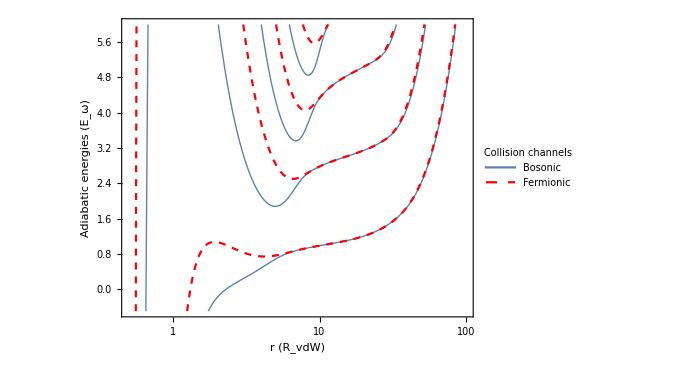

```mathematica
LogLinearPlot[{1/Ω(Take[Sort[Eigenvalues[V[x]]],Lmax/2+1]-ref),1/Ω(Take[Sort[Eigenvalues[V2[x]]],Lmax/2]-Take[ref,Lmax/2])},{x,0.5,xf},
PlotRange->{-0.5,6},AxesOrigin->{0.5,0},
AspectRatio->0.75,
Frame->True, FrameStyle->{{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]},{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]}},
PlotStyle->{Thick,{Red,Dashed}},PlotLegends->Placed[LineLegend[{Style["Bosonic",FontFamily->"Times",FontWeight->Bold],Style["Fermionic",FontFamily->"Times",FontWeight->Bold]}, LegendLabel->Style["Collision channels",FontSize->14, FontFamily->"Times",FontWeight->Bold],LegendFunction->(Framed[#,RoundingRadius->0,Background->White]&),LegendMargins->5],{Left,Top}],FrameLabel->{Style["r (R_vdW)",FontSize->20, FontFamily->"Times New Roman",FontWeight->Bold],Style["Adiabatic energies (E_ω)",FontSize->20,FontWeight->Bold, FontFamily->"Times"]},GridLines->Automatic, GridLinesStyle->Directive[Thin, Dashed, LightGray],ImagePadding->50,ImageSize->500]
```

Subroutine determining final point of integration versus energy. This speeds up the numerical calculations. The plot shows final point of integration versus Log[10,-E]

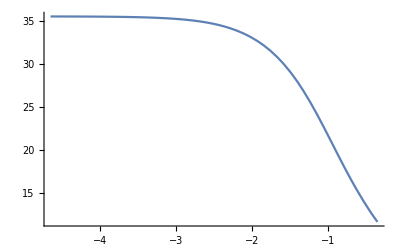

```mathematica
Module[{pemin,pemax,dp,TurnPoint,k,ExpInt,p,x,tabf},TurnPoint[e_?NumericQ]:=x/.FindRoot[e+1/x^6-αz x^2==0,{x,xi,xf}][[1]];(*Przybliżenie WKB*)
k[x_,e_]:=Sqrt[-(e+1/x^6-αz x^2)];
ExpInt[rf_?NumericQ,e_?NumericQ]:=NIntegrate[k[x,e],{x,TurnPoint[e],rf}];
pemin=Log[10,-emin];
pemax=Log[10,-emax];
tabf=Table[{p,x/.FindRoot[Exp[-ExpInt[x,-10^p]]==epsf,{x,TurnPoint[-10^p],xf}][[1]]},{p,pemin,pemax,(pemax-pemin)/nptf}];xfin=Interpolation[tabf];
Plot[xfin[x],{x,pemin,pemax}]]
```

Subroutine determining steps
Parameters:
npt -  number of points per one wave-lenght

InterpolatingFunction::dmval: Input value {0.100039} lies outside the range of data in the interpolating function. Extrapolation will be used.

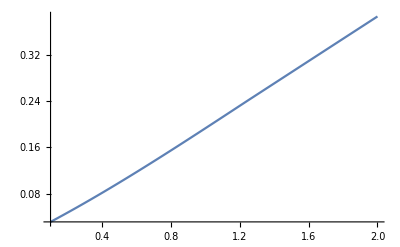

```mathematica
Module[{tab,eig,lambda,h,dbl,n},

tab=Table[eig=Eigenvalues[V[x]];{x,Min[Flatten[{2Pi/Sqrt[Abs[emin-eig]],2Pi/Sqrt[Abs[emax-eig]]}]]},{x,xi,xf,(xf-xi)/nptl}];
lambda=Interpolation[tab]; (*Local de Broglie wavelength (minimum over all channels). Used for determination of the step size *)

xt={};
h=lambda[xi]/npt;
AppendTo[xt,xi];
AppendTo[xt,xi+h];
dbl=1; (* dbl = 1 - step doubling or halving was done in the previous step, dbl = 0 otherwise *)
n=2;

While[(xt[[n]]<xf)||(dbl==1),
Which[
(lambda[xt[[n]]]≥2 npt h)&&(dbl==0),

h=2h;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

(lambda[xt[[n]]]<npt h)&&(dbl==0),

h=h/2;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

True,

AppendTo[xt,xt[[n]]+h];
dbl=0;
];
n++;
];
nstep=n;  (* Total number of steps *);
Plot[lambda[x],{x,0.1,2},PlotRange->All]
]
```

Number of steps

```mathematica
nstep
```

3147

Matching point (somewhere between xi and xf in the classically allowed regime). It position is determined versus position of the classical turning point for highest L

```mathematica
xmid=(x/.FindRoot[Sort[Eigenvalues[V[x]]][[1]]-ref[[1]]==emax,{x,xi,xf}][[1]])
```

1.33945

Location of the matching point in the table xt

```mathematica
nmid=1; 
While[xt[[nmid]]<xmid,nmid++];
nmid--
xt[[nmid]]
```

238

1.33597

Subroutine performing outward integration using renormalized Numerov method
It takes Psi0 as an initial condition

Parameters:
en - energy
n0 -  starting point (element of xt)
nf -  final point (element of xt)
phi - short-range phase
cl: if 1 clears table Rout (to save memory)

```mathematica
evolNumOut[en_?NumericQ,n0_?IntegerQ,nf_?IntegerQ,phi_?NumericQ,cl_?IntegerQ]:=
Module[{W,Qt,n,Rinv,h,h0,nodes,Ro},

nodes=0;

Rout[n0]=Psi0[xt[[n0+1]],phi].Inverse[Psi0[xt[[n0]],phi]];
nodes+=Length[Select[Eigenvalues[Rout[n0]],#<0&]];(*Which functions change sign*)
h=xt[[n0+1]]-xt[[n0]];
n=n0+1;

While[n<=nf,
h0=h;
h=xt[[n+1]]-xt[[n]];
Which[

Abs[h]>1.5 Abs[h0],
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].(2 Id -(5h^2/6)QT[[n]]-(Id+(h^2/12)QT[[n-2]]).Inverse[Rout[n-1].Rout[n-2]]);,

Abs[h]<0.75 Abs[h0],
Qt=(en + ref[[1]])Id-V[(xt[[n]]+xt[[n-1]])/2];
Rinv=Inverse[2 Id-(h0^2/12)Qt].((Id+(h0^2/12)QT[[n-1]]).Inverse[Rout[n-1]]+Id+(h0^2/12)QT[[n]]);
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)Qt).Rinv);,

True,
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)QT[[n-1]]).Inverse[Rout[n-1]]);
];
nodes+=Length[Select[Eigenvalues[Rout[n]],#<0&]];
n++;
];
Ro=Rout[nf];
Clear[W,Qt,n,Rinv,h,h0];
If[cl==1,Clear[Rout]];
{Ro,nodes}]
```

Subroutine performing inward integration using renormalized Noumerov method
It assumes that function vanishes at the starting value

Parameters:
Parameters:
en - energy
n0 -  starting point (element of xt)
nf -  final point (element of xt)
cl: if 1 clears table Rout (to save memory)

```mathematica
evolNumIn[en_?NumericQ,n0_?IntegerQ,nf_?IntegerQ,cl_?IntegerQ]:=
Module[{W,Qt,n,Rinv,h,h0,nodes,Ri},

nodes=0;
h=xt[[n0-2]]-xt[[n0-1]];
W=Id+(h^2/12) QT[[n0-2]];
Rin[n0-1]=Inverse[W].(2 Id -(5h^2/6)QT[[n0-1]]);
nodes+=Length[Select[Eigenvalues[Rin[n0-1]],#<0&]];
n=n0-2;

While[n>=nf,
h0=h;
h=xt[[n-1]]-xt[[n]];
Which[

Abs[h]>1.5 Abs[h0],
W=Id+(h^2/12) QT[[n-1]];
Rin[n]=Inverse[W].(2 Id -(5h^2/6)QT[[n]]-(Id+(h^2/12)QT[[n+2]]).Inverse[Rin[n+1].Rin[n+2]]);,

Abs[h]<0.75 Abs[h0],
Qt=(en+ref[[1]]) Id-V[(xt[[n]]+xt[[n+1]])/2];
Rinv=Inverse[2 Id-(h0^2/12)Qt].((Id+(h0^2/12)QT[[n+1]]).Inverse[Rin[n+1]]+Id+(h0^2/12)QT[[n]]);
W=Id+(h^2/12) QT[[n-1]];
Rin[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)Qt).Rinv);,

True,
W=Id+(h^2/12) QT[[n-1]];
Rin[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)QT[[n+1]]).Inverse[Rin[n+1]]);
];
nodes+=Length[Select[Eigenvalues[Rin[n]],#<0&]];
n--;
];
Ri=Rin[nf];
Clear[W,Qt,n,Rinv,h,h0];
If[cl==1,Clear[Rin]];
{Ri,nodes}]
```

Subroutine calculating determinant that should vanish at the matching point if the energy is correct

Parameters:
en -  energy
phi -  short range phase

```mathematica
EigenEn[en_?NumericQ,phi_?NumericQ]:=
Module[{n,win,wout,nodes,det,m,nmax},
QT=Table[(en+ref[[1]]) Id-V[xt[[n]]],{n,1,Length[xt]}];
nmax=nstep;
While[xt[[nmax]]>xfin[Log[10,-en]],nmax--];
win=evolNumIn[en,nmax,nmid+1,1]; (* Performs inward integration *)
wout=evolNumOut[en,1,nmid,phi,1];  (* Performs outward integration *)
nodes=win[[2]]+wout[[2]]; (* Total number of nodes *) 
m=wout[[1]]-Inverse[win[[1]]];
det=Det[m]; (*Calculates determinant that should vanish at the the matching point *)
Clear[n,win,wout,QT];
{det,nodes,m}
]
```

```mathematica
Timing[EigenEn[-3.,Pi/4]]
```

InterpolatingFunction::dmval: Input value {0.477121} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.15625,{8.2978×10^-12,13,{{0.0428273,-0.0020037,0.00030834,0.0000231547,8.07874×10^-7,1.70296×10^-8,2.42066×10^-10,2.48062×10^-12,1.91984×10^-14,1.16163×10^-16,5.64486×10^-19,2.25104×10^-21,7.498×10^-24,2.11721×10^-26,5.13202×10^-29,1.07946×10^-31,1.98876×10^-34},{-0.0020036,0.0541821,-0.00294872,-0.0000394965,-6.10879×10^-7,-7.30149×10^-9,-6.29602×10^-11,-3.75632×10^-13,-1.3656×10^-15,-7.46642×10^-19,2.75042×10^-20,2.19518×10^-22,1.06318×10^-24,3.86785×10^-27,1.13381×10^-29,2.77444×10^-32,5.79356×10^-35},{0.000308384,-0.00294873,0.0823031,-0.00201906,-0.0000146078,-1.43826×10^-7,-1.2831×10^-9,-9.68294×10^-12,-6.08791×10^-14,-3.19182×10^-16,-1.40489×10^-18,-5.23694×10^-21,-1.66844×10^-23,-4.58337×10^-26,-1.09471×10^-28,-2.29075×10^-31,-4.22928×10^-34},{0.00002316,-0.000039498,-0.00201907,0.113653,-0.00150355,-6.38482×10^-6,-3.88011×10^-8,-2.21327×10^-10,-1.10101×10^-12,-4.68438×10^-15,-1.699×10^-17,-5.26848×10^-20,-1.40456×10^-22,-3.24043×10^-25,-6.51363×10^-28,-1.14832×10^-30,-1.78654×10^-33},{8.08154×10^-7,-6.10936×10^-7,-0.0000146084,-0.00150355,0.145884,-0.00119896,-3.39142×10^-6,-1.44354×10^-8,-5.97597×10^-11,-2.22577×10^-13,-7.29127×10^-16,-2.08791×10^-18,-5.22741×10^-21,-1.1477×10^-23,-2.21934×10^-26,-3.79851×10^-29,-5.78398×10^-32},{1.70379×10^-8,-7.30252×10^-9,-1.43845×10^-7,-6.385×10^-6,-0.00119896,0.178585,-0.00099685,-2.01286×10^-6,-6.36693×10^-9,-2.01123×10^-11,-5.84556×10^-14,-1.52401×10^-16,-3.53495×10^-19,-7.2829×10^-22,-1.33447×10^-24,-2.18062×10^-27,-3.18876×10^-30},{2.42225×10^-10,-6.29691×10^-11,-1.28345×10^-9,-3.88045×10^-8,-3.3915×10^-6,-0.000996854,0.211571,-0.000853221,-1.29007×10^-6,-3.15953×10^-9,-7.89055×10^-12,-1.84566×10^-14,-3.9329×10^-17,-7.56008×10^-20,-1.30712×10^-22,-2.03296×10^-25,-2.84889×10^-28},{2.48273×10^-12,-3.75624×10^-13,-9.68727×10^-12,-2.21369×10^-10,-1.44364×10^-8,-2.0129×10^-6,-0.000853224,0.244755,-0.000746078,-8.75084×10^-7,-1.71087×10^-9,-3.46863×10^-12,-6.68345×10^-15,-1.18812×10^-17,-1.92702×10^-20,-2.84024×10^-23,-3.80132×10^-26},{1.92188×10^-14,-1.36445×10^-15,-6.09195×10^-14,-1.10136×10^-12,-5.97693×10^-11,-6.36734×10^-9,-1.2901×10^-6,-0.000746081,0.278096,-0.000663201,-6.20084×10^-7,-9.91162×10^-10,-1.66557×10^-12,-2.69279×10^-15,-4.05961×10^-18,-5.63708×10^-21,-7.1749×10^-24},{1.16314×10^-16,-7.30855×10^-19,-3.19472×10^-16,-4.68662×10^-15,-2.2264×10^-13,-2.01151×10^-11,-3.15971×10^-9,-8.75099×10^-7,-0.000663203,0.311575,-0.000597261,-4.54889×10^-7,-6.06032×10^-10,-8.58412×10^-13,-1.18211×10^-15,-1.53186×10^-18,-1.8433×10^-21},{5.65363×10^-19,2.76348×10^-20,-1.40656×10^-18,-1.70011×10^-17,-7.29443×10^-16,-5.84703×10^-14,-7.89155×10^-12,-1.71096×10^-9,-6.20094×10^-7,-0.000597263,0.345183,-0.000543603,-3.43238×10^-7,-3.8726×10^-10,-4.68865×10^-13,-5.5689×10^-16,-6.27374×10^-19},{2.25516×10^-21,2.20302×10^-22,-5.24476×10^-21,-5.27298×10^-20,-2.08919×10^-18,-1.52461×10^-16,-1.84608×10^-14,-3.46903×10^-12,-9.9121×10^-10,-4.54896×10^-7,-0.000543606,0.378918,-0.000499133,-2.65106×10^-7,-2.56728×10^-10,-2.68835×10^-13,-2.78346×10^-16},{7.51397×10^-24,1.06683×10^-24,-1.67149×10^-23,-1.40605×10^-22,-5.23166×10^-21,-3.53694×10^-19,-3.93432×10^-17,-6.68484×10^-15,-1.66574×10^-12,-6.0606×10^-10,-3.43244×10^-7,-0.000499135,0.412781,-0.000461712,-2.08819×10^-7,-1.75574×10^-10,-1.60631×10^-13},{2.12239×10^-26,3.88161×10^-27,-4.59337×10^-26,-3.24459×10^-25,-1.14889×10^-23,-7.28842×10^-22,-7.56404×10^-20,-1.18852×10^-17,-2.69331×10^-15,-8.58498×10^-13,-3.87277×10^-10,-2.65111×10^-7,-0.000461714,0.446777,-0.000429815,-1.67258×10^-7,-1.2332×10^-10},{5.14633×10^-29,1.13811×10^-29,-1.09752×10^-28,-6.52347×10^-28,-2.22215×10^-26,-1.33577×10^-24,-1.30805×10^-22,-1.92796×10^-20,-4.06087×10^-18,-1.18232×10^-15,-4.68909×10^-13,-2.56739×10^-10,-2.08823×10^-7,-0.000429818,0.480911,-0.00040233,-1.35914×10^-7},{1.08286×10^-31,2.78578×10^-32,-2.29754×10^-31,-1.15033×10^-30,-3.80426×10^-29,-2.18325×10^-27,-2.03484×10^-25,-2.84214×10^-23,-5.63966×10^-21,-1.5323×10^-18,-5.56984×10^-16,-2.68859×10^-13,-1.75581×10^-10,-1.67261×10^-7,-0.000402332,0.51519,-0.000378422},{1.99578×10^-34,5.81922×10^-35,-4.24362×10^-34,-1.79009×10^-33,-5.79427×10^-32,-3.19339×10^-30,-2.85217×10^-28,-3.80465×10^-26,-7.17945×10^-24,-1.8441×10^-21,-6.27547×10^-19,-2.78391×10^-16,-1.60645×10^-13,-1.23326×10^-10,-1.35916×10^-7,-0.000378424,0.54962}}}}

```mathematica
detphi[ph_?NumericQ,en_?NumericQ]:=Module[{wout,m,det},
wout=evolNumOut[en,1,nmid,ph,1];
m=wout[[1]]-Inverse[win[[1]]];
det=Det[m]; (*Calculates determinant that should vanish at the the matching point *)
Clear[wout];
{det,m}]
```

Subroutine determining roots with the renormalized Noumerov method

Parameters:
en - energy of bound state
nst - 

Output:
tabsol -  table containing eigenenergies
tabm -  table of corresponding matrices that are used to dermine eigenvectors (null space vectors)

```mathematica
RootsF[en_?NumericQ,nst_?NumericQ]:=
Module[{nmax,tab,phi,n,xn,fn,tabR,tabsol,tabm,fun,x,tabv},
QT=Table[(en+ref[[1]]) Id-V[xt[[n]]],{n,1,Length[xt]}];
nmax=nstep;
While[xt[[nmax]]>xfin[Log[10,-en]],nmax--];
win=evolNumIn[en,nmax,nmid+1,1]; (* Performs inward integration *)
tab=Table[{phi,detphi[phi,en]},{phi,phimin,phimax,Pi/nst}];
tabR={};
fun[x_?NumericQ]:=detphi[x,en][[1]];
For[n=1,n<Length[tab],n++,
If[(tab[[n,2,1]]tab[[n+1,2,1]]<=0),
xn=(tab[[n+1,1]]+tab[[n,1]])/2;
fn=fun[xn];
If[(tab[[n,2,1]]-fn)(tab[[n+1,2,1]]-fn)<0,AppendTo[tabR,{tab[[n,1]],tab[[n+1,1]]}]];
]
];
tabsol=Table[x/.FindRoot[fun[x]==0,{x,tabR[[n,1]],tabR[[n,2]]},Method->"Brent",PrecisionGoal->9][[1]],{n,1,Length[tabR]}];
tabm=Table[detphi[tabsol[[n]],en][[2]],{n,1,Length[tabsol]}];
tabv=Table[NullSpace[tabm[[n]],Tolerance->10^-4][[1]],{n,1,Length[tabm]}];
Clear[tab,nmax,phi,n,xn,fn,tabR,fun,x,QT];
(*Print["tabsol=",tabsol]*);
{tabsol,tabv}]
```

```mathematica
RootsFOld[phi_?NumericQ,emn_?NumericQ,emx_?NumericQ]:=
Module[{tab,tabnew,tabR,pemin,pemax,dp=0.005,fun,tabsol,x,tabm,tabv},
pemin=Log[10,-emn];
pemax=Log[10,-emx];
tabnew=Table[{pen,EigenEn[-10^pen,phi]},{pen,pemin,pemax,dp}];
tabR={};
fun[x_?NumericQ]:=EigenEn[-10^x,phi][[1]];
Do[If[(tabnew[[n,2,1]]tabnew[[n+1,2,1]]<0)&&(tabnew[[n,2,2]]==tabnew[[n+1,2,2]]),AppendTo[tabR,{tabnew[[n,1]],tabnew[[n+1,1]]}]],{n,1,Length[tabnew]-1}];
tab=Table[{tabnew[[n,1]],tabnew[[n,2,1]]},{n,1,Length[tabnew]}];
tabsol=Table[x/.FindRoot[fun[x]==0,{x,tabR[[n,1]],tabR[[n,2]]},Method->"Brent"][[1]],{n,1,Length[tabR]}];
tabm=Table[EigenEn[-10^tabsol[[n]],phi][[3]],{n,1,Length[tabsol]}];
{tabsol,tabm}]
```

```mathematica
ash[phi_]:=(Pi/8)(1+Tan[phi])/Gamma[5/4]^2
ϕ[a_]:=ArcTan[-((8*Gamma[5/4]^2)/π a-1)];
```

Subroutine calculating the wave function at the grid points in xt

Parameters:
phi - short-range phase
vec -  corerespondin eigenvector (value of the wave function at the matching point)

```mathematica
CalcPsi[phi_?NumericQ,en_?NumericQ,vecp_]:=Module[{win,wout,n,pe,nmax},
pe=Log[10,-en];
QT=Table[(en+ref[[1]]) Id-V[xt[[n]]],{n,1,Length[xt]}];
nmax=nstep;
While[xt[[nmax]]>xfin[pe],nmax--];
win=evolNumIn[en,nmax,nmid+1,0]; (* Performs inward integration *)
wout=evolNumOut[en,1,nmid,phi,0];  (* Performs outward integration *)
Psi[nmid]=vecp;
Do[Psi[n]=Inverse[Rout[n]].Psi[n+1],{n,nmid-1,1,-1}];
Do[Psi[n]=Inverse[Rin[n]].Psi[n-1],{n,nmid+1,nmax-1}];
Psi[nmax]=0 Id.Psi[nmax-1];
Do[Psi[n]=0 Id.Psi[n-1];,{n,nmax+1,nstep}];
]
```

```mathematica
rts={};
dp=0.1;
Module[{pemin,pemax,pen,tabp,p},
pemin=Log[10,-emin];
pemax=Log[10,-emax];
tabp={};
p=pemin;
While[p≤pemax,AppendTo[tabp,p];p+=dp];
Print[tabp];
Print["Progress:"];
Print[ProgressIndicator[Dynamic[n],{1,Length[tabp]}]];
Do[en=-10^tabp[[i]];
If[And[i<=-0.0016,i>=-0.0030],Print["Pass"],
(*Print["en = ",en];*)
n=i;

bound=(x/.FindRoot[Sort[Eigenvalues[V[x]]][[1]]==en,{x,0.2, 1000}]);
xf = 5bound;
xmid = xi+ (bound-xi)/2;
nmid=1; 
While[xt[[nmid]]<xmid,nmid++];
nmid--;

(*Print["xi = ",xi, " xf = ",xf," xmid = ", xmid];*)


AppendTo[rts, {-10^tabp[[i]],RootsF[-10^tabp[[i]],1000]}]]

,{i,1,Length[tabp]}
]
]
```

{-4.65667,-4.55667,-4.45667,-4.35667,-4.25667,-4.15667,-4.05667,-3.95667,-3.85667,-3.75667,-3.65667,-3.55667,-3.45667,-3.35667,-3.25667,-3.15667,-3.05667,-2.95667,-2.85667,-2.75667,-2.65667,-2.55667,-2.45667,-2.35667,-2.25667,-2.15667,-2.05667,-1.95667,-1.85667,-1.75667,-1.65667,-1.55667,-1.45667,-1.35667,-1.25667,-1.15667,-1.05667,-0.956666,-0.856666,-0.756666,-0.656666,-0.556666,-0.456666,-0.356666}

Progress:

```mathematica
taben={};tabphi={};tabvec={};
Do[AppendTo[taben,{aHOz/ash[rts[[n,2,1,m]]],1/Ωz rts[[n,1]]}];AppendTo[tabphi,{rts[[n,2,1,m]],rts[[n,1]]}];AppendTo[tabvec,rts[[n,2,2,m]]],{n,1,Length[rts]},{m,1,Length[rts[[n,2,1]]]}];
```

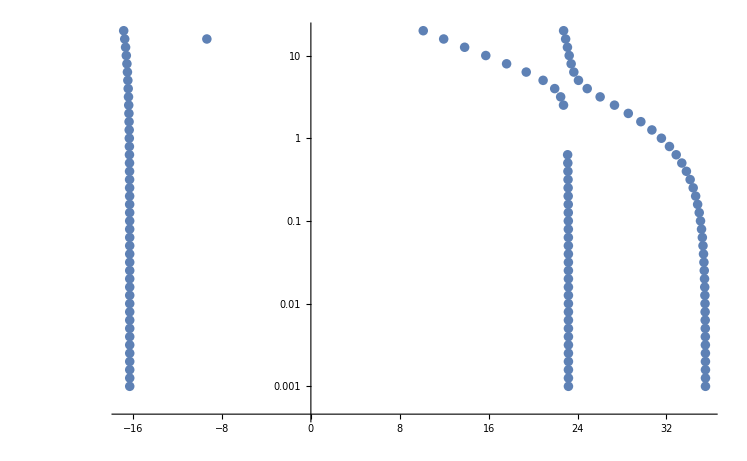

{{-23.1764,-0.001},{-35.5085,-0.001},{16.3004,-0.001},{-23.1764,-0.00125893},{-35.5073,-0.00125893},{16.3004,-0.00125893},{-23.1763,-0.00158489},{-35.5058,-0.00158489},{16.3004,-0.00158489},{-23.1763,-0.00199526},{-35.5039,-0.00199526},{16.3004,-0.00199526},{-23.1762,-0.00251189},{-35.5015,-0.00251189},{16.3004,-0.00251189},{-23.1762,-0.00316228},{-35.4985,-0.00316228},{16.3004,-0.00316228},{-23.1761,-0.00398107},{-35.4948,-0.00398107},{16.3005,-0.00398107},{-23.176,-0.00501187},{-35.49,-0.00501187},{16.3005,-0.00501187},{-23.1758,-0.00630957},{-35.4841,-0.00630957},{16.3006,-0.00630957},{-23.1757,-0.00794328},{-35.4766,-0.00794328},{16.3006,-0.00794328},{-23.1754,-0.01},{-35.4672,-0.01},{16.3007,-0.01},{-23.1752,-0.0125893},{-35.4553,-0.0125893},{16.3008,-0.0125893},{-23.1748,-0.0158489},{-35.4404,-0.0158489},{16.3009,-0.0158489},{-23.1744,-0.0199526},{-35.4216,-0.0199526},{16.3011,-0.0199526},{-23.1739,-0.0251189},{-35.3981,-0.0251189},{16.3013,-0.0251189},{-23.1732,-0.0316228},{-35.3684,-0.0316228},{16.3015,-0.0316228},{-23.1723,-0.0398107},{-35.3312,-0.0398107},{16.3019,-0.0398107},{-23.1712,-0.0501187},{-35.2845,-0.0501187},{16.3023,-0.0501187},{-23.1698,-0.0630957},{-35.2259,-0.0630957},{16.3028,-0.0630957},{-23.1681,-0.0794328},{-35.1525,-0.0794328},{16.3034,-0.0794328},{-23.1659,-0.1},{-35.0605,-0.1},{16.3042,-0.1},{-23.1631,-0.125893},{-34.9456,-0.125893},{16.3052,-0.125893},{-23.1595,-0.158489},{-34.8023,-0.158489},{16.3065,-0.158489},{-23.155,-0.199526},{-34.6238,-0.199526},{16.308,-0.199526},{-23.1493,-0.251189},{-34.4023,-0.251189},{16.31,-0.251189},{-23.1419,-0.316228},{-34.1282,-0.316228},{16.3125,-0.316228},{-23.1324,-0.398107},{-33.7907,-0.398107},{16.3156,-0.398107},{-23.1201,-0.501187},{-33.3773,-0.501187},{16.3195,-0.501187},{-23.1041,-0.630957},{-32.8742,-0.630957},{16.3244,-0.630957},{-32.267,-0.794328},{16.3304,-0.794328},{-31.5416,-1.},{16.338,-1.},{-30.6858,-1.25893},{16.3473,-1.25893},{-29.6922,-1.58489},{16.3589,-1.58489},{-28.5627,-1.99526},{16.3731,-1.99526},{-22.7338,-2.51189},{-27.3192,-2.51189},{16.3906,-2.51189},{-22.4763,-3.16228},{-26.0294,-3.16228},{16.412,-3.16228},{-21.9403,-3.98107},{-24.8658,-3.98107},{16.438,-3.98107},{-20.8963,-5.01187},{-24.0787,-5.01187},{16.4694,-5.01187},{-19.3785,-6.30957},{-23.6611,-6.30957},{16.5074,-6.30957},{-17.6113,-7.94328},{-23.4203,-7.94328},{16.553,-7.94328},{-15.7385,-10.},{-23.2443,-10.},{16.6076,-10.},{-13.8363,-12.5893},{-23.0862,-12.5893},{16.6729,-12.5893},{-11.9505,-15.8489},{-22.9235,-15.8489},{16.751,-15.8489},{9.36066,-15.8489},{-10.1114,-19.9526},{-22.7418,-19.9526},{16.8442,-19.9526}}

```mathematica
ListLogPlot[-taben,PlotRange->All]
taben
```

```mathematica
emin = -emin; emax = -emax;
```

```mathematica
rts1={};
Module[{pemin,pemax,pen,tabe,p},
tabe={};
dp=0.0008 emax;
p=emin;
While[p≤emax,AppendTo[tabe,p];p+=dp];
(*Print[tabe];*)
Print["Progress:"];
Print[ProgressIndicator[Dynamic[k],{1,Length[tabe]}]];
Do[en=tabe[[i]];
(*Print["en = ",en];*)
k=i;
bound=(x/.FindRoot[Sort[Eigenvalues[V[x]]][[1]]==en,{x,0.2, 1000}]);
xf = 5bound;
xmid = xi+ (bound-xi)/2;
nmid=1; 
While[xt[[nmid]]<xmid,nmid++];
nmid--;

(*Print["xi = ",xi, " xf = ",xf," xmid = ", xmid];*)


AppendTo[rts1, {tabe[[i]],RootsF[tabe[[i]],500]}]

,{i,1,Length[tabe]}
]
]
```

Progress:

```mathematica
taben1={};tabphi1={};tabvec1={};
Do[AppendTo[taben1,{aHOz/ash[rts1[[n,2,1,m]]],1/Ωz rts1[[n,1]]}];AppendTo[tabphi1,{rts1[[n,2,1,m]],rts1[[n,1]]}];AppendTo[tabvec1,rts1[[n,2,2,m]]],{n,1,Length[rts1]},{m,1,Length[rts1[[n,2,1]]]}];
```

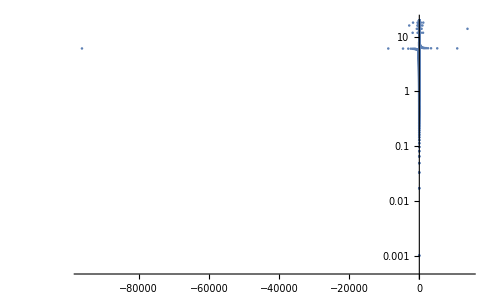

{{-23.1764,-0.001},{-35.5085,-0.001},{16.3004,-0.001},{-23.1764,-0.00125893},{-35.5073,-0.00125893},{16.3004,-0.00125893},{-23.1763,-0.00158489},{-35.5058,-0.00158489},{16.3004,-0.00158489},{-23.1763,-0.00199526},{-35.5039,-0.00199526},{16.3004,-0.00199526},{-23.1762,-0.00251189},{-35.5015,-0.00251189},{16.3004,-0.00251189},{-23.1762,-0.00316228},{-35.4985,-0.00316228},{16.3004,-0.00316228},{-23.1761,-0.00398107},{-35.4948,-0.00398107},{16.3005,-0.00398107},{-23.176,-0.00501187},{-35.49,-0.00501187},{16.3005,-0.00501187},{-23.1758,-0.00630957},{-35.4841,-0.00630957},{16.3006,-0.00630957},{-23.1757,-0.00794328},{-35.4766,-0.00794328},{16.3006,-0.00794328},{-23.1754,-0.01},{-35.4672,-0.01},{16.3007,-0.01},{-23.1752,-0.0125893},{-35.4553,-0.0125893},{16.3008,-0.0125893},{-23.1748,-0.0158489},{-35.4404,-0.0158489},{16.3009,-0.0158489},{-23.1744,-0.0199526},{-35.4216,-0.0199526},{16.3011,-0.0199526},{-23.1739,-0.0251189},{-35.3981,-0.0251189},{16.3013,-0.0251189},{-23.1732,-0.0316228},{-35.3684,-0.0316228},{16.3015,-0.0316228},{-23.1723,-0.0398107},{-35.3312,-0.0398107},{16.3019,-0.0398107},{-23.1712,-0.0501187},{-35.2845,-0.0501187},{16.3023,-0.0501187},{-23.1698,-0.0630957},{-35.2259,-0.0630957},{16.3028,-0.0630957},{-23.1681,-0.0794328},{-35.1525,-0.0794328},{16.3034,-0.0794328},{-23.1659,-0.1},{-35.0605,-0.1},{16.3042,-0.1},{-23.1631,-0.125893},{-34.9456,-0.125893},{16.3052,-0.125893},{-23.1595,-0.158489},{-34.8023,-0.158489},{16.3065,-0.158489},{-23.155,-0.199526},{-34.6238,-0.199526},{16.308,-0.199526},{-23.1493,-0.251189},{-34.4023,-0.251189},{16.31,-0.251189},{-23.1419,-0.316228},{-34.1282,-0.316228},{16.3125,-0.316228},{-23.1324,-0.398107},{-33.7907,-0.398107},{16.3156,-0.398107},{-23.1201,-0.501187},{-33.3773,-0.501187},{16.3195,-0.501187},{-23.1041,-0.630957},{-32.8742,-0.630957},{16.3244,-0.630957},{-32.267,-0.794328},{16.3304,-0.794328},{-31.5416,-1.},{16.338,-1.},{-30.6858,-1.25893},{16.3473,-1.25893},{-29.6922,-1.58489},{16.3589,-1.58489},{-28.5627,-1.99526},{16.3731,-1.99526},{-22.7338,-2.51189},{-27.3192,-2.51189},{16.3906,-2.51189},{-22.4763,-3.16228},{-26.0294,-3.16228},{16.412,-3.16228},{-21.9403,-3.98107},{-24.8658,-3.98107},{16.438,-3.98107},{-20.8963,-5.01187},{-24.0787,-5.01187},{16.4694,-5.01187},{-19.3785,-6.30957},{-23.6611,-6.30957},{16.5074,-6.30957},{-17.6113,-7.94328},{-23.4203,-7.94328},{16.553,-7.94328},{-15.7385,-10.},{-23.2443,-10.},{16.6076,-10.},{-13.8363,-12.5893},{-23.0862,-12.5893},{16.6729,-12.5893},{-11.9505,-15.8489},{-22.9235,-15.8489},{16.751,-15.8489},{9.36066,-15.8489},{-10.1114,-19.9526},{-22.7418,-19.9526},{16.8442,-19.9526}}

```mathematica
ListLogPlot[taben1,PlotRange->All]
taben
```

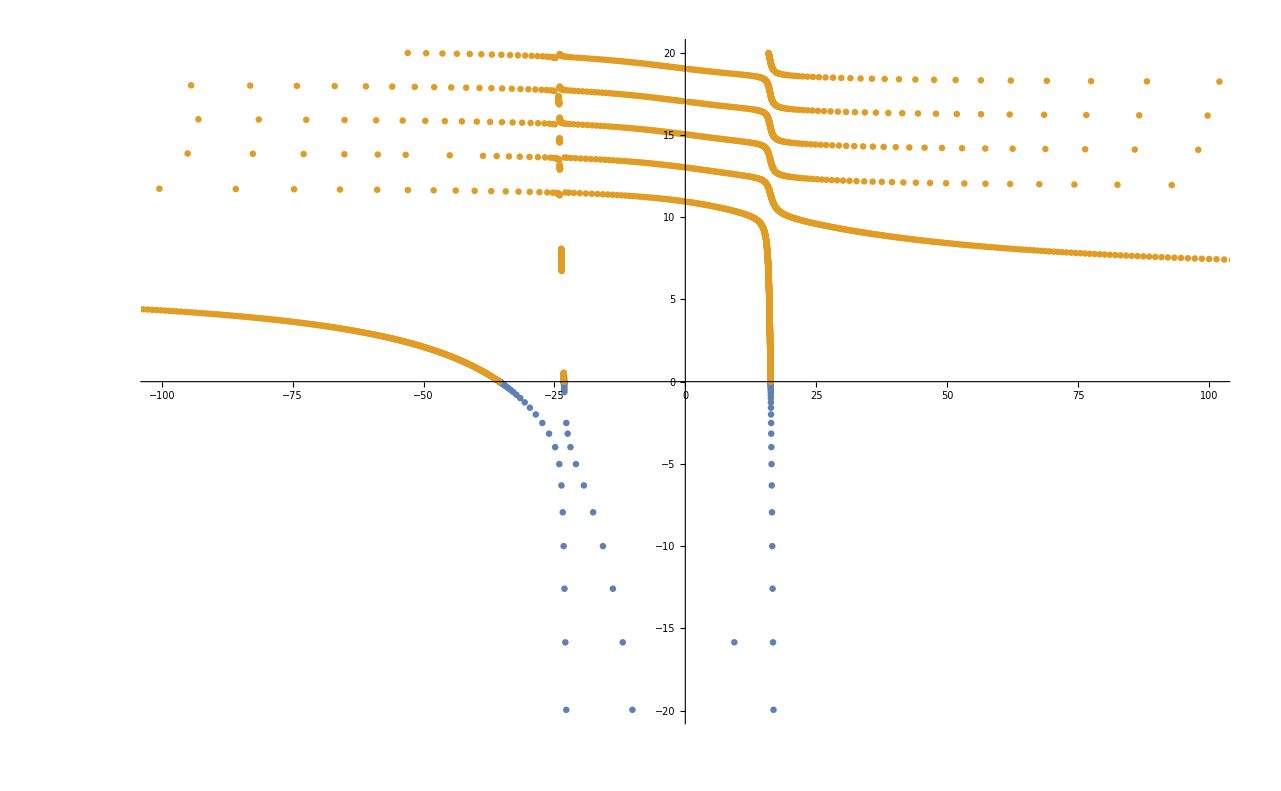

```mathematica
ListPlot[{taben,taben1},PlotRange->{{-100,100},{-20,20}}]
```

```mathematica
Export["Drop_3D_30_07.csv",Join[taben,taben1]]
```

Drop_3D_30_07.csv

```mathematica
tabb=Join[taben,taben1];
```

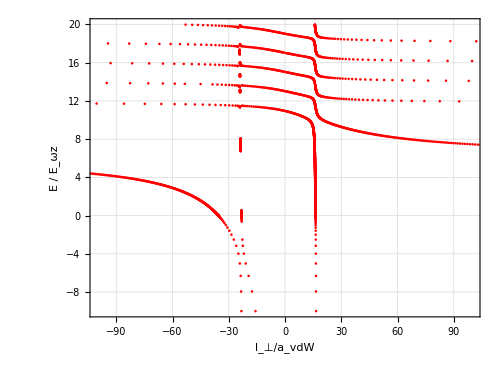

```mathematica
ListPlot[tabb,PlotRange->{{-100,100},{-10,20}},
AspectRatio->0.75,
Frame->True, FrameStyle->{{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]},{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]}},
PlotStyle->{Thick,{Red,Dashed}},FrameLabel->{Style["l_⊥/a_vdW",FontSize->20, FontFamily->"Times New Roman",FontWeight->Bold],Style["E / E_ωz",FontSize->20,FontWeight->Bold, FontFamily->"Times"]},GridLines->Automatic, GridLinesStyle->Directive[Thin, Dashed, LightGray],ImagePadding->50,ImageSize->500]
```

```mathematica
new=FindCurvePath[tabb.{{1,0},{0,100}}];
new1=Join[tabb[[#]]&/@new];
```

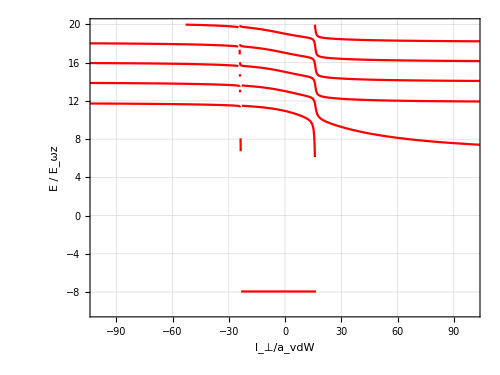

```mathematica
ListLinePlot[new1,PlotRange->{{-100,100},{-10,20}},
AspectRatio->0.75,
Frame->True, FrameStyle->{{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]},{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]}},
PlotStyle->Red,FrameLabel->{Style["l_⊥/a_vdW",FontSize->20, FontFamily->"Times New Roman",FontWeight->Bold],Style["E / E_ωz",FontSize->20,FontWeight->Bold, FontFamily->"Times"]},GridLines->Automatic, GridLinesStyle->Directive[Thin, Dashed, LightGray],ImagePadding->50,ImageSize->500]
```

```mathematica
tabela=Import["Drop_3D_30_07_2.csv"]
```

Import::nffil: File Drop_3D_30_07_2.csv not found during Import.

$Failed